```mathematica
mirrorv[tile_]:=Module[{line={},tMirror={}},
tMirror={};
For[i=1,i≤Length[tile],i++,
line={};
For[j=Length[tile[[1]]],j≥1,j--,
AppendTo[line,tile[[i,j]]];
];
AppendTo[tMirror,line];
];
tMirror
]
```

```mathematica
rotatec[tile_]:=Module[{line={},tMirror={}},
tMirror={};
For[i=1,i≤Length[tile[[1]]],i++,
line={};
For[j=Length[tile],j≥1,j--,
AppendTo[line,tile[[j,i]]];
];
AppendTo[tMirror,line];
];
tMirror
]
```

```mathematica
allTiles[tile_]:=Module[{list={}},
list=Join[NestList[rotatec,tile,3],
NestList[rotatec,mirrorv[tile],3]];
list=DeleteDuplicates[list];
list
]
```

```mathematica
tiles={
{{1}},
{{1,1}},
{{1,0},
{1,1}},
{{1,1,1}},
{{1,1},
{1,1}},
{{0,1,0},
{1,1,1}},
{{1,0,0},
{1,1,1}},
{{1,1,1,1}},
{{0,1,1}, 
{1,1,0}}
}
```

{{{1}},{{1,1}},{{1,0},{1,1}},{{1,1,1}},{{1,1},{1,1}},{{0,1,0},{1,1,1}},{{1,0,0},{1,1,1}},{{1,1,1,1}},{{0,1,1},{1,1,0}}}

```mathematica
tiles=Flatten[allTiles/@tiles,1];
```

```mathematica
ArrayPlot[#,ImageSize->100,Frame->None,Mesh -> True, ColorRules->{0->Transparent,1->Table[Part[{Red,Yellow,Green, Purple, Orange, LightBlue, Blue, Pink, LightOrange},RandomInteger[8]+1], 9]}]&/@tiles
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PolyominoGraph[arrayMesh_]:=Construct[With[{edges=ReplaceAll[MeshPrimitives[#,1],Line[x_]:>UndirectedEdge@@Round[x]]},Graph[edges,VertexCoordinates->(#->#&/@Union[edges/. UndirectedEdge->Sequence])]]&,arrayMesh]
```

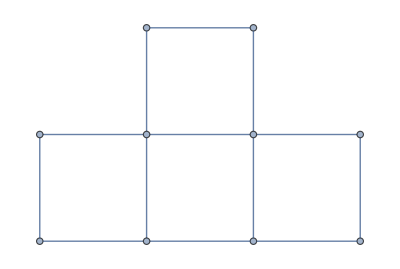

```mathematica
form=PolyominoGraph[ArrayMesh[tiles[[11]]]]
```

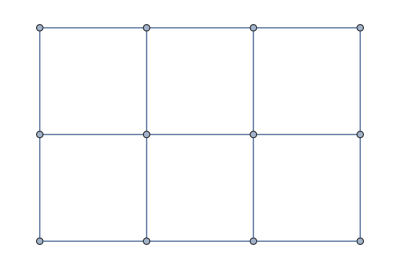

```mathematica
emptiness=PolyominoGraph[ArrayMesh[ConstantArray[1,{2,3}]]]
```

```mathematica
PolyominoCoverMatrix[forms_,emptiness_]:=With[{form4Cycles=Map[Sort,FindCycle[#,{4},All]&/@Flatten[FindIsomorphicSubgraph[emptiness,#,All]&/@forms],3],emptiness4Cycles=Map[Sort,FindCycle[emptiness,{4},All],2]},MapThread[Join,{IdentityMatrix[Length@form4Cycles],Function[{cycles},ReplacePart[Array[0&,Length@emptiness4Cycles],#->1&/@Flatten[Position[emptiness4Cycles,#]&/@cycles]]]/@form4Cycles}]]
```

```mathematica
CoverGraph[coverMatrix_]:=ResourceFunction["NestWhileGraph"][Function[{state},Select[state+#&/@coverMatrix,!MemberQ[#,2]&]],{ConstantArray[0,Last[Dimensions[coverMatrix]]]},UnsameQ@@#&,2]
```

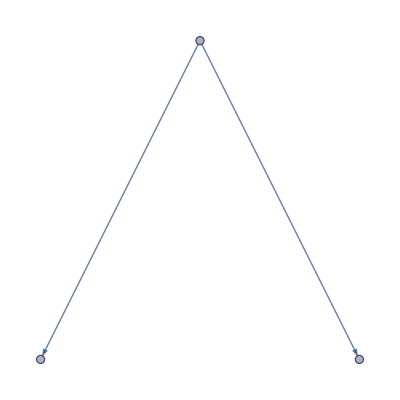

```mathematica
CoverGraph[PolyominoCoverMatrix[{form},emptiness]]
```

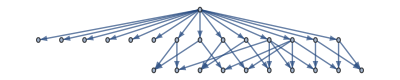

```mathematica
CoverGraph[PolyominoCoverMatrix[{form},PolyominoGraph[ArrayMesh[ConstantArray[1,{3,4}]]]]]
```